```mathematica
f[x_,y_,gap_,phase_]:=NIntegrate[Sin[Sqrt[x^2+(y-t)^2]+phase]/gap,{t,-gap/2,gap/2}]
```

```mathematica
Plot3D[f[x,y,8,0],{x,0,16},{y,-18,18},ColorFunction->"TemperatureMap",Mesh->None,PlotPoints->15]
```

-Graphics3D-

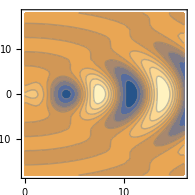

```mathematica
ContourPlot[f[x,y,8,0],{x,0,16},{y,-18,18},ContourStyle->Gray,PlotPoints->15]
```

```mathematica
Export["E:\\gap=2.gif",Table[Plot3D[f[x,y,2,phase],{x,0,16},{y,-18,18},ColorFunction->"TemperatureMap",Mesh->None,PlotPoints->15],{phase,2Pi,0,-Pi/12}]]
Export["E:\\gap=8.gif",Table[Plot3D[f[x,y,8,phase],{x,0,16},{y,-18,18},ColorFunction->"TemperatureMap",Mesh->None,PlotPoints->15],{phase,2Pi,0,-Pi/12}]]
Export["E:\\gap=2-8.gif",Table[Plot3D[f[x,y,gap,0],{x,0,16},{y,-18,18},ColorFunction->"TemperatureMap",Mesh->None,PlotPoints->15],{gap,1,8,0.5}]]
```